# 1D Invasion Sport Model

## Utilities

```mathematica
lightBeige = RGBColor[1.,0.9920042725261311,0.8800030518043793];
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> lightBeige]
```

```mathematica
ClearAll["Global`*"]
```

## Functions

### Visualizations

```mathematica
showRoute[route_]:= Module[{frames},
ListAnimate[getPlot/@ route, DefaultDuration->1, AnimationRepetitions->1]
]
```

```mathematica
getPlot[state_, bstart_]:= showFrame@getFrame[state, bstart]
```

```mathematica
showFrame[frame_]:= ArrayPlot[frame, ColorRules->colorRules, AspectRatio->1/12, ImageSize->175]
```

```mathematica
getFrame[{attackers_, defenders_, ball_}, bstart_]:= Module[{anum, dnum, aparts, dparts, pparts}, 
{anum, dnum } = If[attackers == defenders, {5, 5}, {1, 2}];
aparts = {#, attackers}->anum&/@ Range[2, 5];
dparts = {#, defenders}->dnum&/@ Range[2, 5];
pparts =  {#, bstart}->4&/@ Range[2, 5];
ReplacePart[gameArray, Join[aparts, dparts,pparts ,{ {1, ball}->3}]
]]
```

```mathematica
showRoute[route_, bstart_]:= getPlot[#, bstart]&/@ route
```

### Game Logic

```mathematica
canGoShortQ[defender_]:=shortPass+(shortPass - ballStart)/ballSpeed - reactionTime < defender
```

```mathematica
canGoLongQ[astart_, dstart_]:= dstart - astart < reactionTime
```

```mathematica
roundDownToOdd[n_]:=Module[{floor},floor=Floor[n];
If[OddQ[floor],floor,floor-1]]
```

```mathematica
getPass[features_]:= Module[{dest, amoves, bmoves, await, bwait, pass},
dest = features["passLoc"];
amoves = Range[features["astart"],  dest, If[dest>features["astart"], playerSpeed,-playerSpeed]];
bmoves = Range[features["bstart"], dest, ballSpeed];
await = If[Length@bmoves > Length@amoves,PadRight[amoves, Length@bmoves, Last[amoves]], amoves];
bwait = If[Length@bmoves < Length@amoves, PadRight[bmoves, Length@amoves,Last[bmoves]], bmoves];
pass = Transpose[{await, bwait}]
]
```

```mathematica
guard[features_]:= Module[{astart, bstart, dstart, bdest, move, delay,ptime, wait},
{astart, bstart, dstart, bdest} = Lookup[features, {"astart", "bstart", "dstart", "passLoc"}];
move = Range[dstart, bdest, If[bdest>dstart, playerSpeed,-playerSpeed]];
delay = Join[Table[dstart, reactionTime],move];
ptime =Max[(Abs[(bdest - astart)] / playerSpeed)+1,((bdest - bstart) / ballSpeed) +1];
wait = PadRight[delay, ptime, Last[delay]]
]
```

```mathematica
getFeatures[ballStart_]:= Module[{lpass, astart, dvariance, dstart, spass, longQ, passLoc}, 
lpass = roundDownToOdd@Min[armStrength+ballStart, courtLength];
astart= Floor[lpass  - ((lpass-ballStart)/ballSpeed)playerSpeed];
dvariance = RandomChoice[{1/3, 1/3, 1/3}->{-1, 0, 3}];
(*dstart =astart+reactionTime+dvariance;*)
dstart =astart+reactionTime;
spass = roundDownToOdd[((dstart+reactionTime-1)ballSpeed+ballStart)/(ballSpeed+1)];
longQ = canGoLongQ[astart, dstart];
passLoc = If[longQ,lpass, spass];
<|"bstart"->ballStart,"passLoc"->passLoc, "astart"->astart, "dstart"->dstart|>
]
```

```mathematica
sowRoute[ballStart_]:=Module[{features, attacker, defender, ball,pass, dlocs, rlocs}, 
features = getFeatures[ballStart];
pass =getPass[features];
dlocs = guard[features];
rlocs = MapThread[Insert[#1, #2, 2]&, {pass, dlocs}];
Sow[rlocs, "route"]; Sow[ballStart, "bstart"];pass[[-1, 2]]
]
```

```mathematica
getRouteChain[n_:10]:= Module[{reaped, routes, bstarts, plots}, 
reaped = Reap[Nest[sowRoute, 1, n], {"route", "bstart"}];
routes = reaped[[2, 1, 1]];
bstarts = reaped[[2, 2, 1]];
plots =  Flatten[MapThread[showRoute[#1, #2]&, {routes, bstarts}], 1]
]
```

```mathematica
getPotentialPlayerStatesSmart[{playerState_, ballState_}]:= Module[{forwardQ, backwardQ,stationaryQ,legalMoves, allPossibleMoves},
If[ballInAirQ[ballState], catch[playerState, ballState[[2]]], 
backwardQ = playerState[[1]]>= (minDistanceToPasser - ballStartPosition)+ballSpeed&&NonPositive[playerState[[2]]];
(*Players need to move more*)
stationaryQ = playerState[[2]] != 0;
forwardQ = playerState[[1]]<=(courtSize - playerSpeed)&& NonNegative[playerState[[2]]];
allPossibleMoves = {{playerState[[1]] - playerSpeed, -playerSpeed}, {playerState[[1]], 0}, {playerState[[1]]+playerSpeed, playerSpeed}};
legalMoves = Flatten@Position[{backwardQ, stationaryQ, forwardQ}, True];
allPossibleMoves[[legalMoves]]
]]
```

### Constants

```mathematica
colorRules = {1->Blue, 2->Red, 3->Green, 4->Black, 5->Purple};
gameArray = ConstantArray[0, {5, courtLength}];
playerSpeed = 1;
ballSpeed = 2;
nPlayers = 3;
```

### Parameters

```mathematica
armStrength = 125;
reactionTime = 5;
courtLength = 125;
```

### Initialization

## Running Code

### Gameplay

```mathematica
frames =  getRouteChain[1];
```

```mathematica
ListAnimate[frames, DefaultDuration->1, AnimationRepetitions->1]
```

### Saving animations

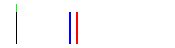
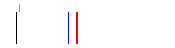
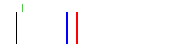
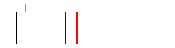
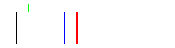
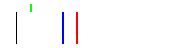
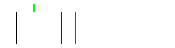
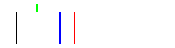

```mathematica
frames
```

```mathematica
dir = "Projects/Wolfram/SummerSchool/InvasionSport1D/"
```

Projects/Wolfram/SummerSchool/InvasionSport1D/

```mathematica
Export[dir<>"r5.gif", frames, OverwriteTarget->False]
```

Projects/Wolfram/SummerSchool/InvasionSport1D/r5.gif

## Analysis

### Arm Strength

```mathematica
spassFunc[armStrength_, courtLength_]:= Module[{ballStart = 1, lpass, astart, dstart, spass}, 
lpass = roundDownToOdd@Min[armStrength+ballStart, courtLength];
astart= Floor[lpass  - ((lpass-ballStart)/ballSpeed)playerSpeed];
dstart =astart+reactionTime;
spass = roundDownToOdd[((dstart+reactionTime-1)ballSpeed+ballStart)/(ballSpeed+1)]
]
```

```mathematica
fs = Callout[spassFunc[as, #], #]&/@ Range[20, 60, 10]
```

{Callout[-1+Floor[1/3 (1+2 (8+Floor[1/2 (2-Floor[Min[20,1+as]])+Floor[Min[20,1+as]]]))],20],Callout[-1+Floor[1/3 (1+2 (8+Floor[1/2 (2-Floor[Min[30,1+as]])+Floor[Min[30,1+as]]]))],30],Callout[-1+Floor[1/3 (1+2 (8+Floor[1/2 (2-Floor[Min[40,1+as]])+Floor[Min[40,1+as]]]))],40],Callout[-1+Floor[1/3 (1+2 (8+Floor[1/2 (2-Floor[Min[50,1+as]])+Floor[Min[50,1+as]]]))],50],Callout[-1+Floor[1/3 (1+2 (8+Floor[1/2 (2-Floor[Min[60,1+as]])+Floor[Min[60,1+as]]]))],60]}

Here we have a plot showing the Longest completed pass possible with a safe-playing defender at different arm strengths and court lengths. The distance scales linearly with arm strength up until the size of the court. Here we can see that increasing ball entropy increases attacker progression

```mathematica
Plot[fs, {as, 3, 100}, PlotHighlighting->None,Frame->{True, True, False, False},FrameLabel->{"Arm Strength", "Pass Distance"}, PlotLabel->"Pass Distance Over Arm Strength at Different Court Lengths"]
```

-Graphics-

```mathematica
Plot3D[spassFunc[as, cl], {as, 3, 100}, {cl, 20, 60}]
```

-Graphics3D-

### Reaction Time

```mathematica
spassFunc[reactionTime_]:= Module[{ballStart = 1, lpass, astart, dstart, spass}, 
lpass = roundDownToOdd@Min[armStrength+ballStart, courtLength];
astart= Floor[lpass  - ((lpass-ballStart)/ballSpeed)playerSpeed];
dstart =astart+reactionTime;
spass = roundDownToOdd[((dstart+reactionTime-1)ballSpeed+ballStart)/(ballSpeed+1)]
]
```

Here we can see reaction time also scales linearly

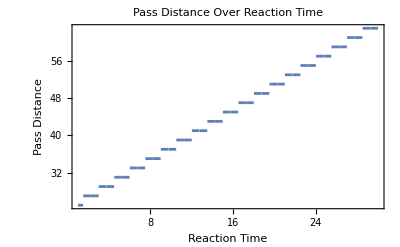

```mathematica
Plot[spassFunc[rt], {rt, 1, 30}, PlotHighlighting->None,Frame->{True, True, False, False},FrameLabel->{"Reaction Time", "Pass Distance"}, PlotLabel->"Pass Distance Over Reaction Time"]
```